## Initialization

### Physical Constants

```mathematica
hsq=41.8015876;
esq=1.4399764;
```

### Differentiation properties

```mathematica
lMax=20;
RMax=20.0;
```

### Central potential definitions

```mathematica
PotentialCoul[R_, {z1_, z2_}, Rcoul_]:=If[
R>Rcoul,
esq(z1 z2)/R,
esq(z1 z2)/(2.Rcoul)(3.-R^2/Rcoul^2)];
WoodsSaxson[R_, {V0_,R0_,a0_}]:=-V0/(1.+Exp[(R-R0)/a0]);
```

### Input parameters

```mathematica
partition=Table[Null,{i,1,10}];
optPar=Table[Null,{i,1,10}];
boundPar=Table[Null,{i,1,10}];
partition⟦1⟧=
{4., 12., 2., 6., 72.0};
(* m1, m2, z1, z2, Elab *)


optPar⟦1⟧={150.0 ,1.938, 0.65,          4.0, 1.938, 0.65,          1.938,  False};
(*V0, Subscript[r, V], Subscript[a, V], W0, Subscript[r, i], Subscript[a, i], Subscript[r, coul], is here r small? *)
```

### Precalculations

```mathematica
setCapitalR[potList_, partNum_]:=
Module[{temp, factor},
factor=partition[[partNum,1]]^(1/3)+partition[[partNum,2]]^(1/3);
temp=potList;
If[temp[[8]],
temp[[2]]=factor temp[[2]];
temp[[5]]=factor temp[[5]];
temp[[7]]=factor temp[[7]];
];
temp
];

Do[
optPar⟦i⟧=setCapitalR[optPar⟦i⟧,i];

,{i,1,1}];
```

## The Scattering State Wave Function

## The Coulomb Functions

```mathematica
CoulombPhase[ℓ_,η_]:=(LogGamma[ℓ+ⅈ η+1]-LogGamma[ℓ-ⅈ η+1])/(2 ⅈ);
CoulombHPlus[ℓ_,ρ_,η_]:=WhittakerW[-ⅈ η,ℓ+1/2,-2 ⅈ ρ] ⅇ^(ⅈ CoulombPhase[ℓ,η]+1/2 π (η-ⅈ ℓ));
CoulombHMinus[ℓ_,ρ_, η_]:=WhittakerW[ⅈ η,ℓ+1/2,2 ⅈ ρ] ⅇ^(1/2 π (η+ⅈ ℓ)-ⅈ CoulombPhase[ℓ,η]);
CoulombFactor[ℓ_,η_]:=(ⅇ^(1/2 (-π) (η+ⅈ (ℓ+1))) √(Gamma[ℓ-ⅈ η+1] Gamma[ℓ+ⅈ η+1]))/(2 (2 ℓ+1)!);
CoulombF[ℓ_,ρ_,η_]:=CoulombFactor[ℓ,η] WhittakerM[ⅈ η,ℓ+1/2,2 ⅈ ρ];
CoulombG[ℓ_,ρ_,η_]:=1/2 (CoulombHMinus[ℓ,ρ,η]+CoulombHPlus[ℓ,ρ,η]);
```

## Solving Schrodinger Equation

```mathematica
Interaction[R_,ksq_, μMfd_,l_, i_]:=ksq-μMfd  WoodsSaxson[R,optPar⟦i,1;;3⟧]-μMfd PotentialCoul[R,partition⟦i, 3;;4⟧, optPar⟦i,7⟧]-(l(l+1))/R^2;
```

```mathematica
ShrodingerEquation[l_, μMfd_, ksq_,  i_]:=NDSolve[{ 
x''[R]+Interaction[R,ksq,μMfd,l,i]x[R]+μMfd  WoodsSaxson[R,optPar⟦i,4;;6⟧]  y[R]==0,
y''[R]+Interaction[R,ksq,μMfd,l,i]y[R]-μMfd  WoodsSaxson[R,optPar⟦i,4;;6⟧]  x[R]==0,
x[0.001]==0.0,
y[0.001]==0.0,
x'[0.001]==0.4,
y'[0.001]==0.4},
{x,y},{R,0.001,RMax}] ;
```

```mathematica
getScatWaveFunction[partNum_]:=
Block[{μ,k,μMfd, ksq,η, potPars, Ε},
μ=(partition⟦partNum,1⟧partition⟦partNum,2⟧ )/ (partition⟦partNum,1⟧+partition⟦partNum,2⟧);
μMfd= (2partition⟦partNum,1⟧partition⟦partNum,2⟧ )/(hsq (partition⟦partNum,1⟧+partition⟦partNum,2⟧)); (* (2 μ)/hsq *)
Ε=(partition⟦partNum,5⟧  partition⟦partNum,2⟧)/(partition⟦partNum,1⟧+partition⟦partNum,2⟧);
k=√((2μ  Ε)/hsq);
ksq=(2μ  Ε)/hsq; (* k^2 *)
η=1/(hsq k) esq  μ  partition⟦partNum,3⟧ partition⟦partNum,4⟧ ;
Table[ShrodingerEquation[l, μMfd, ksq, partNum],{l,0,lMax}]
];
```

```mathematica
listOfSolutions=Table[getScatWaveFunction[partNum],{partNum,1,1}];//AbsoluteTiming
```

{1.34589,Null}

```mathematica
waveFunctionRe[partNum_,l_,r_]:=First[Evaluate[x[r]/.listOfSolutions[[partNum,l+1]]]];
waveFunctionIm[partNum_,l_,r_]:=First[Evaluate[y[r]/.listOfSolutions[[partNum,l+1]]]];
```

## S matrix

```mathematica
(*Off[General::munfl];*)
getSmatrix[ partNum_]:=Block[
{r1,r2,x1,x2,y1,y2,
F1,F2,G1,G2,
a,b,c,d,A,B,C1,D1,K1,M,
μ, Ε, k, η},
μ=(partition⟦partNum,1⟧partition⟦partNum,2⟧ )/ (partition⟦partNum,1⟧+partition⟦partNum,2⟧);
Ε=(partition⟦partNum,5⟧  partition⟦partNum,2⟧)/(partition⟦partNum,1⟧+partition⟦partNum,2⟧);
k=√((2μ  Ε)/hsq);
η=1/(hsq k) esq  μ  partition⟦partNum,3⟧ partition⟦partNum,4⟧ ;
r1=19.900001;
r2=RMax 0.8;
Table[
x1=waveFunctionRe[partNum,l,r1];
y1=waveFunctionIm[partNum,l,r1];
F1=Re[CoulombF[l,k r1, η]];
G1=Re[CoulombG[l,k r1,η]];
If[False,
(*False - By derivative of functions, 
True - By arbitrary two points in functions *)
x2=waveFunctionRe[partNum,l,r2];
y2=waveFunctionIm[partNum,l,r2];
F2=CoulombF[l,k r2,η];
G2=CoulombG[l,k r2,η];,
y2=D[waveFunctionIm[partNum,l,r], r] /. r->r1;
x2=D[waveFunctionRe[partNum,l,r], r] /. r->r1;
F2=Re[D[CoulombF[l,k r,η], r] /. r->r1];
G2=Re[D[CoulombG[l,k r,η], r] /. r->r1];];
Print[l,"\t",G1,"\t","\t", G2,"\t", F1,"\t", F2];
a=x2 F1-x1 F2;
b=y1 G2- y2 G1;
c=y2 F1- y1 F2;
d=x1 G2-x2 G1;
A=b-a;
B=-c-d;
C1=a+b;
D1=c-d;
K1=(A C1 + B D1)/(A^2+B^2);
M=(A D1 - B C1)/(A^2+ B^2);
K1+ⅈ M
,{l,0,lMax}]
] ; 
sMatrix=Table[getSmatrix[plotPartNum],{plotPartNum,1,1}]; // AbsoluteTiming
```

0	-0.951574		-0.884561	0.320381	-2.62791

1	-0.112649		-2.7548	0.997888	-0.311207

2	0.937374		-0.996742	0.361205	2.58596

3	0.542017		2.33253	-0.846382	1.4941

4	-0.733795		1.89332	-0.687776	-2.01945

5	-0.808456		-1.64736	0.599648	-2.22177

6	0.442922		-2.48206	0.905007	1.21412

7	0.973709		0.720594	-0.263631	2.66412

8	-0.0639135		2.75065	-1.00811	-0.173556

9	-1.00033		0.41209	-0.151135	-2.72088

10	-0.372763		-2.55417	0.942364	-1.0116

11	0.827647		-1.58944	0.588138	2.23433

12	0.780361		1.75458	-0.652877	2.09969

13	-0.420132		2.48837	-0.929209	-1.12304

14	-1.01282		-0.368006	0.138943	-2.69833

15	-0.172033		-2.67708	1.01051	-0.458241

16	0.906755		-1.27846	0.484371	2.38741

17	0.760943		1.81975	-0.695974	1.99429

18	-0.38746		2.49631	-0.959378	-1.00434

19	-1.03832		-0.0198671	0.00924047	-2.68111

20	-0.390722		-2.47454	0.966329	-1.00537

{2.45083,Null}

```mathematica
sMatrix[[1,1;;3]]
```

{0.515211+0.578863 ⅈ,0.765171-0.128809 ⅈ,0.44608-0.637156 ⅈ}

## Differential Cross Section Of Elastic Scattering

```mathematica
(*amplitudeOfCoulScattering[theta_]:=1/(2 ⅈ k)Sum[(2l+1)(Exp[2ⅈ CoulombPhase[l]]-1)LegendreP[l,Cos[theta]],{l,0,5}];
amplitudeOfCoul[theta_]:=-η/(2 k Sin[1/2 theta]^2)Exp[-ⅈ η Log[Sin[ 1/2 theta]^2]+2 ⅈ Arg[Gamma[1+ⅈ η]]];
amplitudeOfNuclear[theta_]:=1/(2 ⅈ k)Sum[(2l+1) Exp[2 ⅈ  CoulombPhase[l] ] (sMatrix[[l+1]]-1)LegendreP[l,Cos[theta]],{l,0,lMax}];*)
```

```mathematica
PlotSMatrix=ListPlot[Abs[sMatrix], AspectRatio->1.0,Frame->True, PlotLabel->"Absolute values Of the S matrix",AxesLabel->{"dσ/dΩ, mb/sr","θ_cm, degree"}] ;
```

```mathematica
amplitudeOfScattering[partNum_,theta_]:=Block[{μ, Ε, k, η, 
coulScatAmpl, nuclScatAmpl},
μ=(partition⟦partNum,1⟧partition⟦partNum,2⟧ )/(partition⟦partNum,1⟧+partition⟦partNum,2⟧);
Ε=(partition⟦partNum,5⟧  partition⟦partNum,2⟧)/(partition⟦partNum,1⟧+partition⟦partNum,2⟧);
k=√((2μ  Ε)/hsq);
η=1/(hsq k) esq  μ  partition⟦partNum,3⟧ partition⟦partNum,4⟧ ;
coulScatAmpl=-η/(2 k Sin[1/2 theta]^2)Exp[-ⅈ η Log[Sin[ 1/2 theta]^2]+2 ⅈ Arg[Gamma[1+ⅈ η]]];
nuclScatAmpl=1/(2 ⅈ k)Sum[(2l+1) Exp[2 ⅈ  CoulombPhase[l,η] ] (sMatrix[[partNum,l+1]]-1)LegendreP[l,Cos[theta]],{l,0,lMax}];

coulScatAmpl+nuclScatAmpl];
diffCrossSection[partNum_,theta_]:=Abs[amplitudeOfScattering[partNum,Pi theta/180]]^2;
```

```mathematica
plotDiffCS=LogPlot[diffCrossSection[1,theta],{theta,3,180}, AspectRatio->1.0, PerformanceGoal->"Speed", Frame->True,FrameTicks->{Automatic,{Table[i,{i,0,180,30}],None}}, PlotLabel->"Differential Cross Section"];
```

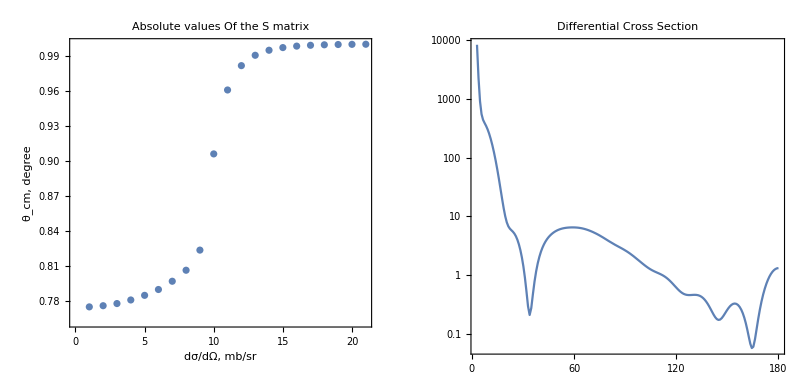

```mathematica
GraphicsRow[{PlotSMatrix, plotDiffCS}]
```

## Normalization Of Wave Functions

```mathematica
normWaveFunctionOf[partNum_]:=Block[{r1,μ, Ε, k, η,
A, B, S1, S2, F, G, x, y,tempList},
r1=0.8RMax ;
μ=(partition⟦partNum,1⟧partition⟦partNum,2⟧ )/ (partition⟦partNum,1⟧+partition⟦partNum,2⟧);
Ε=(partition⟦partNum,5⟧  partition⟦partNum,2⟧)/(partition⟦partNum,1⟧+partition⟦partNum,2⟧);
k=√((2μ  Ε)/hsq);
η=1/(hsq k) esq  μ  partition⟦partNum,3⟧ partition⟦partNum,4⟧ ;
tempList={};
Do[
S1=Re[sMatrix⟦partNum,l+1⟧];
S2=Im[sMatrix⟦partNum,l+1⟧];
F=CoulombF[l,k r1,η];
G=CoulombG[l,k r1,η];
x=waveFunctionRe[partNum,l,r1];
y=waveFunctionIm[partNum,l,r1];
A=(1+S1)F + S2 G;
B=(1-S1) G + S2 F;
AppendTo[tempList,(A x + B y)/(x^2+y^2)+ⅈ (B x + A y)/(x^2+y^2)],{l,0,lMax}];
tempList

];
listOfNorms=Table[normWaveFunctionOf[i],{i,1,3}]; // AbsoluteTiming
```

{2.02972,Null}

```mathematica
normWaveFunction[partNum_,l_,r_]:=Re[listOfNorms⟦partNum,l+1⟧]waveFunctionRe[partNum,l,r]-Im[listOfNorms⟦partNum,l+1⟧]waveFunctionIm[partNum,l,r]+
ⅈ(Re[listOfNorms⟦partNum,l+1⟧]waveFunctionIm[partNum,l,r]+Im[listOfNorms⟦partNum,l+1⟧]waveFunctionRe[partNum,l,r]);
```

### Plot The Partial Wave Functions

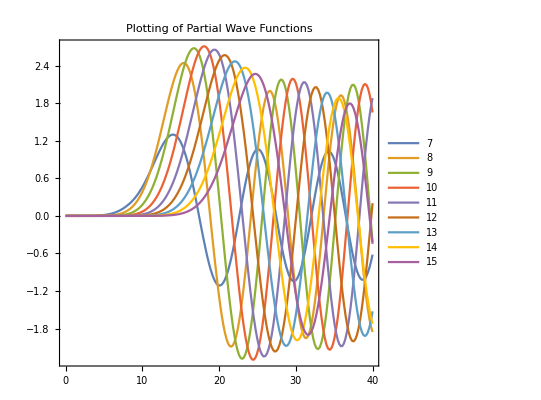

```mathematica
plotlMin=7;
plotlMax=15;
plotPartialWaveFunctions=Plot[Evaluate[Table[Re[normWaveFunction[2,l,r]],{l,plotlMin,plotlMax}]],{r,0.01,RMax}, PerformanceGoal->"Speed", PlotRange->All,Frame->True,AspectRatio->1,PlotLabel->"Plotting of Partial Wave Functions", PlotLegends->{Table[IntegerString[ i],{i,plotlMin,plotlMax}]}]
```

## The Bound State Wave Function

## Schrodinger Equation For Bound State

```mathematica
InteractionBound[R_,ksq_, μMfd_,l_, i_]:=ksq-μMfd  WoodsSaxson[R,boundPar⟦i,1;;3⟧]-(l(l+1))/R^2;
ShrodingerEquationBound[l_, μMfd_, ksq_,  i_]:=NDSolve[{ 
x''[R]+InteractionBound[R,ksq,μMfd,l,i]x[R]==0,
x[20.001]==Exp[-√ksq 20.001],
x'[20.001]==-√ksq Exp[-√ksq 20.001]
},
{x},{R,0.001,RMax}] ;

getBoundWaveFunction[partNum_]:=
Block[{μ,k,μMfd, ksq,η, potPars, Ε},
μ=(partition⟦partNum,1⟧partition⟦partNum,2⟧ )/ (partition⟦partNum,1⟧+partition⟦partNum,2⟧);
μMfd= (2partition⟦partNum,1⟧partition⟦partNum,2⟧ )/(hsq (partition⟦partNum,1⟧+partition⟦partNum,2⟧)); (* (2 μ)/hsq *)
Ε=(partition⟦partNum,5⟧  partition⟦partNum,2⟧)/(partition⟦partNum,1⟧+partition⟦partNum,2⟧);
k=√((2μ  Ε)/hsq);
ksq=(2μ  Ε)/hsq; (* k^2 *)
η=1/(hsq k) esq  μ  partition⟦partNum,3⟧ partition⟦partNum,4⟧ ;
Table[ShrodingerEquationBound[l, μMfd, ksq, partNum],{l,0,0}]
];
```

```mathematica
{0.873,0.767,0.791} 12^(1/3)
```

{1.99867,1.75599,1.81094}